## Base functions

```mathematica
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#}&/@nei,{n,1}->a]
];
graphToNet[g_Graph,ini_List]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,Length[g]],i,out},
For[i=1,i≤Length[g],i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
ret
];
(*add takes the output from remove and builds the new marble distribution*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
(*Print[out];*)
marbles[[-1]]+out
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,{i,T}
];
marbles
]
```

## Triangle

#### No lights - all marbles @ node 1

```mathematica
tri=graphToNet[Graph[{1<->2,2<->3,3<->1}],{3,1}]
```

{{3,{2,3}},{0,{1,3}},{0,{1,2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=netEvolve[tri,ω,ϕ,30000];
```

$Aborted

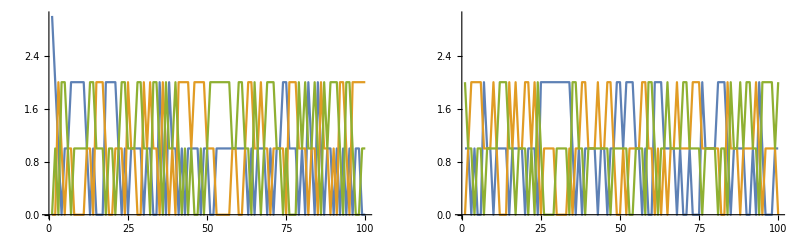

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[tri]}],PlotRange->{0,3}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[tri]}],PlotRange->{0,3}]}}]
```

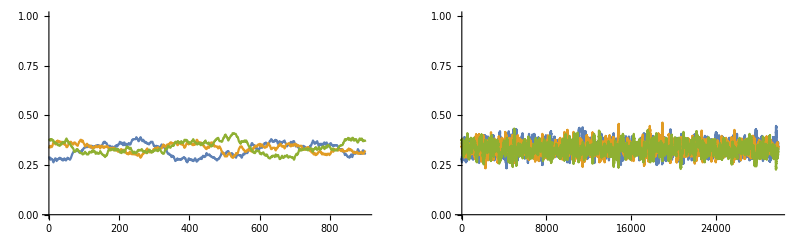

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/3)[[1;;1000]],100],i],{i,Length[tri]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/3,100],i],{i,Length[tri]}],PlotRange->{0,1}]}}]
```

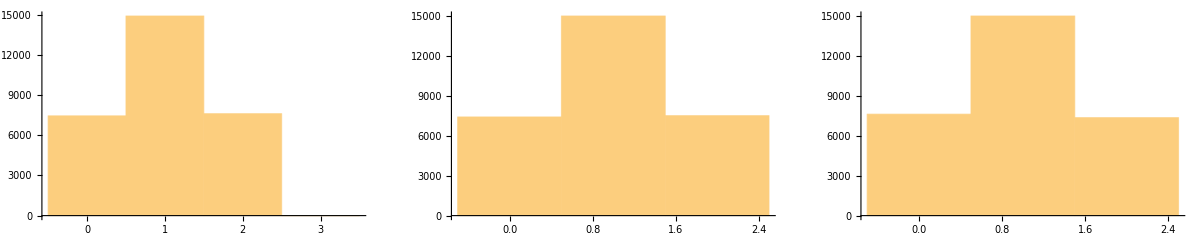

```mathematica
GraphicsGrid[{{Histogram[marbles[[All,1]]],Histogram[marbles[[All,2]]],Histogram[marbles[[All,3]]]}}]
```

```mathematica
Table[{i+1000,Around[Mean[marbles[[All,1]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,1]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}]
```

{{1000,1.00.7},{2000,0.90.7},{3000,1.00.7},{4000,1.00.7},{5000,1.00.7},{6000,1.00.7},{7000,1.00.7},{8000,1.00.7},{9000,1.00.7},{10000,1.00.7},{11000,1.00.7},{12000,1.10.7},{13000,1.00.7},{14000,1.00.7},{15000,1.00.7},{16000,1.00.7},{17000,1.00.7},{18000,1.00.7},{19000,1.00.7},{20000,1.00.7},{21000,1.00.7},{22000,1.00.7},{23000,1.00.7},{24000,1.00.7},{25000,1.00.7},{26000,1.00.7},{27000,1.00.7},{28000,1.00.7},{29000,1.00.7},{30000,1.00.7}}

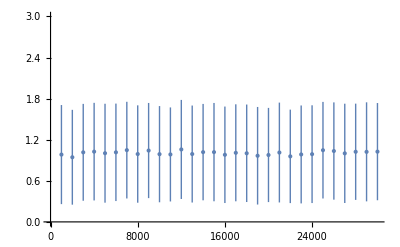

```mathematica
ListPlot[%,PlotRange->{0,3}]
```

## Line

#### No lights - all marbles @ node 1

```mathematica
line=graphToNet[Graph[{1<->2,2<->3}],{3,1}]
```

{{3,{2}},{0,{1,3}},{0,{2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=netEvolve[line,ω,ϕ,30000];
```

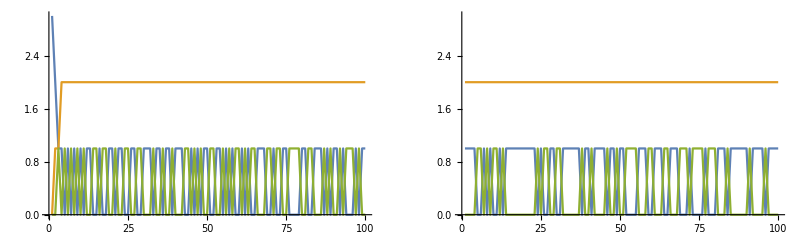

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[tri]}],PlotRange->{0,3}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[tri]}],PlotRange->{0,3}]}}]
```

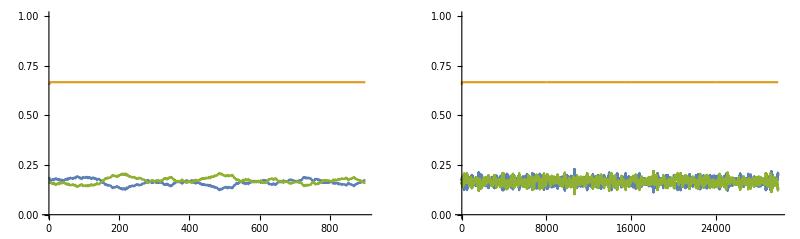

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/3)[[1;;1000]],100],i],{i,Length[tri]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/3,100],i],{i,Length[tri]}],PlotRange->{0,1}]}}]
```

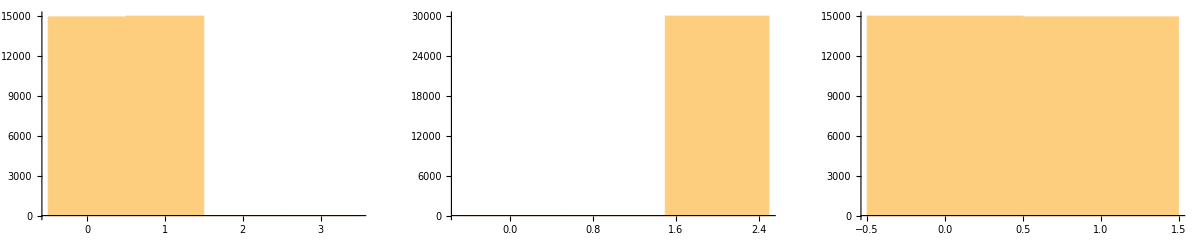

```mathematica
GraphicsGrid[{{Histogram[marbles[[All,1]]],Histogram[marbles[[All,2]]],Histogram[marbles[[All,3]]]}}]
```

```mathematica
devs={Table[{i+1000,Around[Mean[marbles[[All,1]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,1]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],Table[{i+1000,Around[Mean[marbles[[All,2]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,2]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],Table[{i+1000,Around[Mean[marbles[[All,3]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,3]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}]};
```

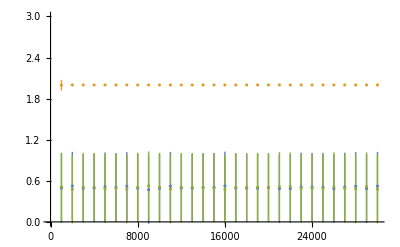

```mathematica
ListPlot[devs,PlotRange->{0,3}]
```

## Long line

#### No lights - all marbles @ node 1

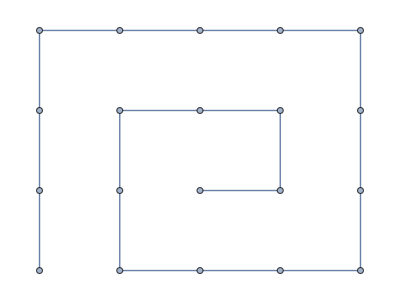

```mathematica
PathGraph[Range[20]]
```

```mathematica
line=graphToNet[PathGraph[Range[20]],{20,1}]
```

{{20,{2}},{0,{1,3}},{0,{2,4}},{0,{3,5}},{0,{4,6}},{0,{5,7}},{0,{6,8}},{0,{7,9}},{0,{8,10}},{0,{9,11}},{0,{10,12}},{0,{11,13}},{0,{12,14}},{0,{13,15}},{0,{14,16}},{0,{15,17}},{0,{16,18}},{0,{17,19}},{0,{18,20}},{0,{19}}}

```mathematica
ω=Table[0,{i,Length[line]},{j,Length[line]}];
ϕ=Table[0,{i,Length[line]},{j,Length[line]}];
marbles=netEvolve[line,ω,ϕ,30000];
```

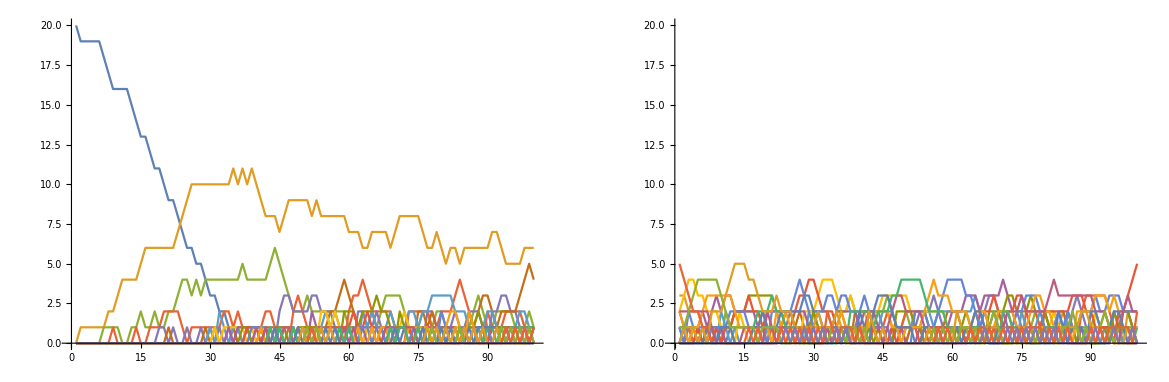

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[line]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[line]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[line]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[line]}],PlotRange->{0,1}]}}]
```

-Graphics-

```mathematica
Partition
```

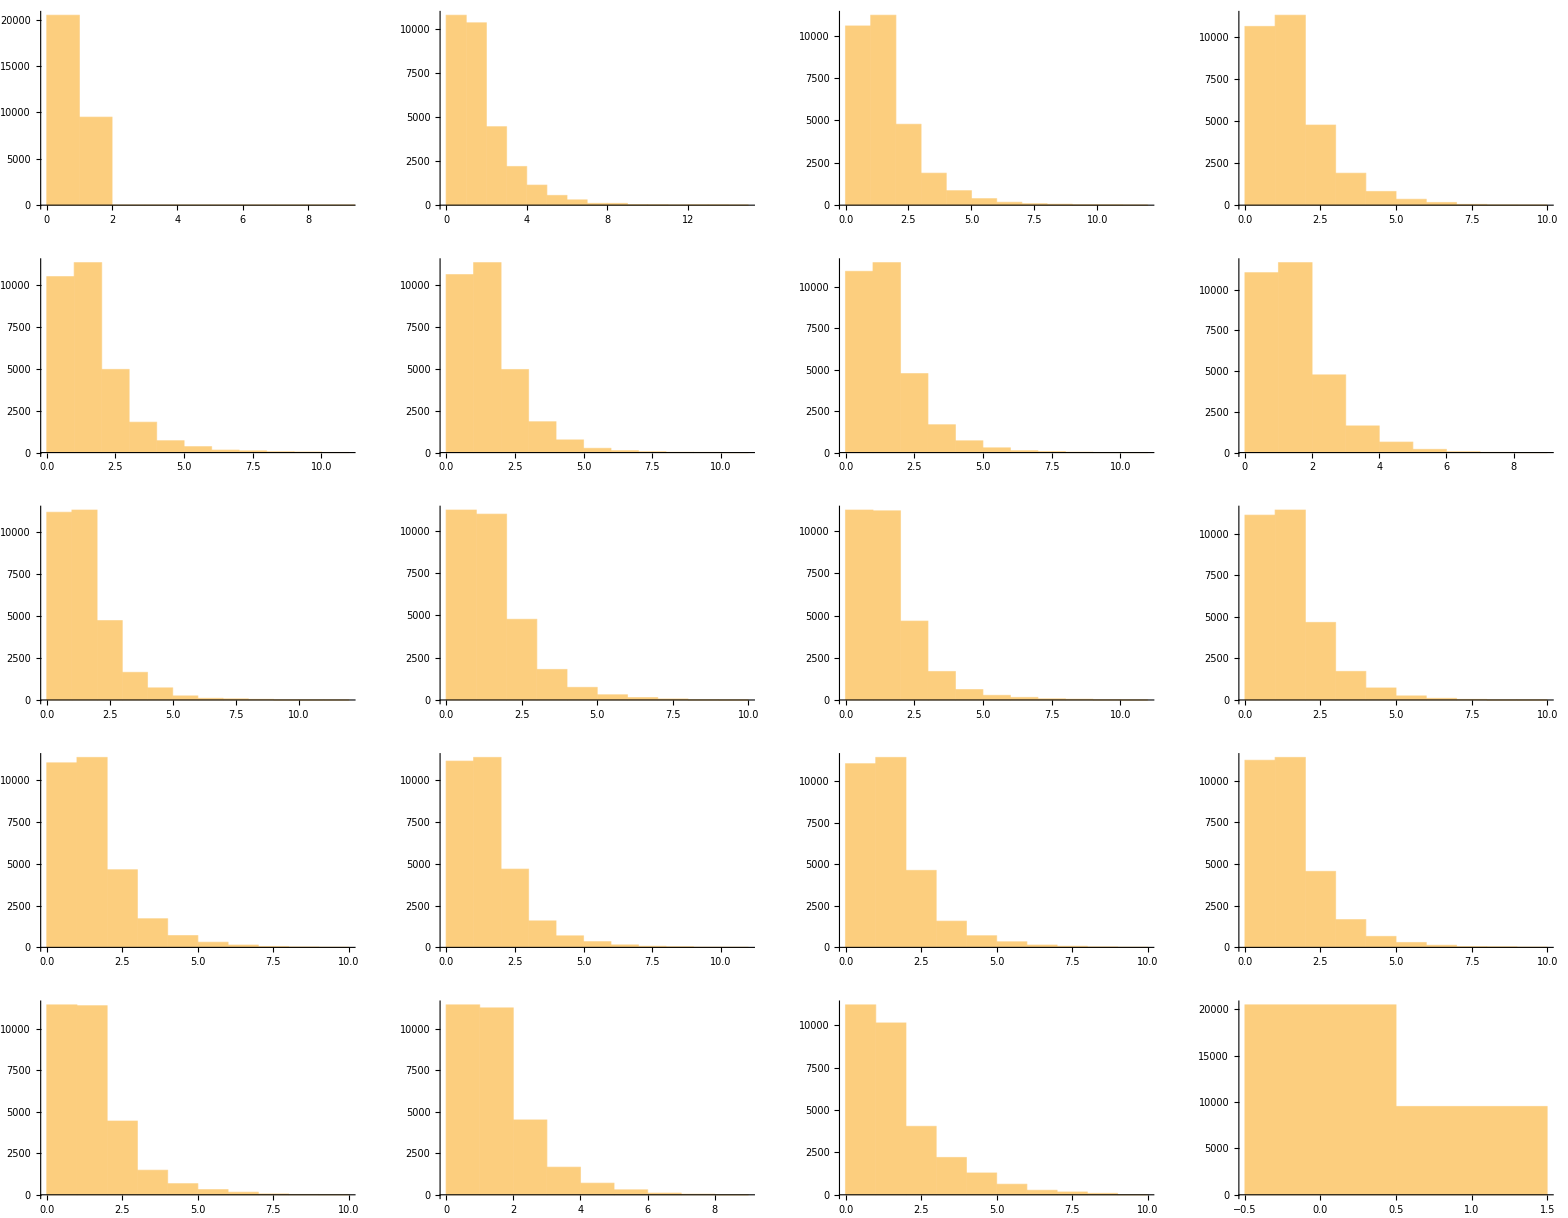

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]]],{i,Length[line]}],4]]
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[line]}];
```

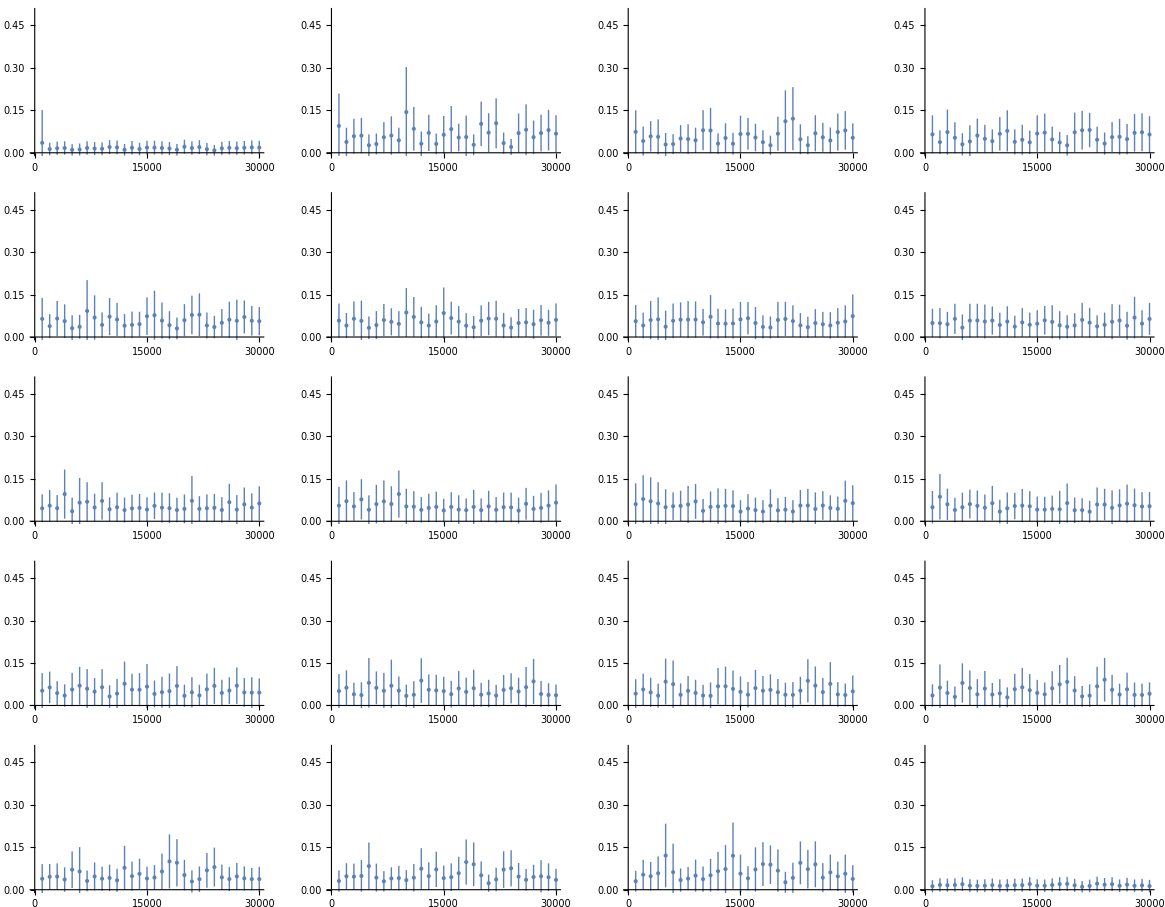

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

## Long cicle

#### No lights - all marbles @ node 1

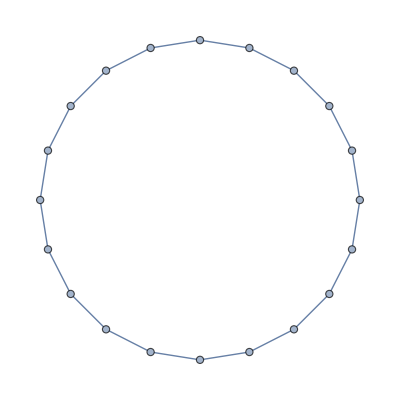

```mathematica
EdgeAdd[PathGraph[Range[20]],20<->1]
```

```mathematica
cicle=graphToNet[EdgeAdd[PathGraph[Range[20]],20<->1],{20,1}]
```

{{20,{2,20}},{0,{1,3}},{0,{2,4}},{0,{3,5}},{0,{4,6}},{0,{5,7}},{0,{6,8}},{0,{7,9}},{0,{8,10}},{0,{9,11}},{0,{10,12}},{0,{11,13}},{0,{12,14}},{0,{13,15}},{0,{14,16}},{0,{15,17}},{0,{16,18}},{0,{17,19}},{0,{18,20}},{0,{1,19}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[cicle,ω,ϕ,30000];
```

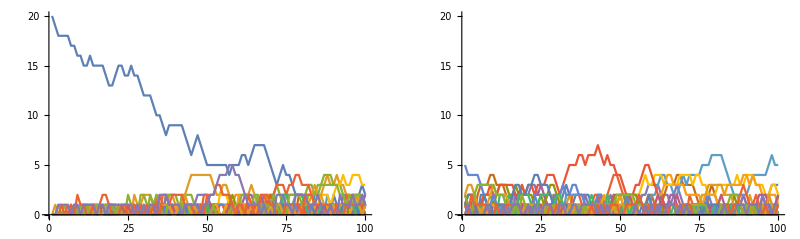

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[cicle]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[cicle]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[cicle]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[cicle]}],PlotRange->{0,1}]}}]
```

-Graphics-

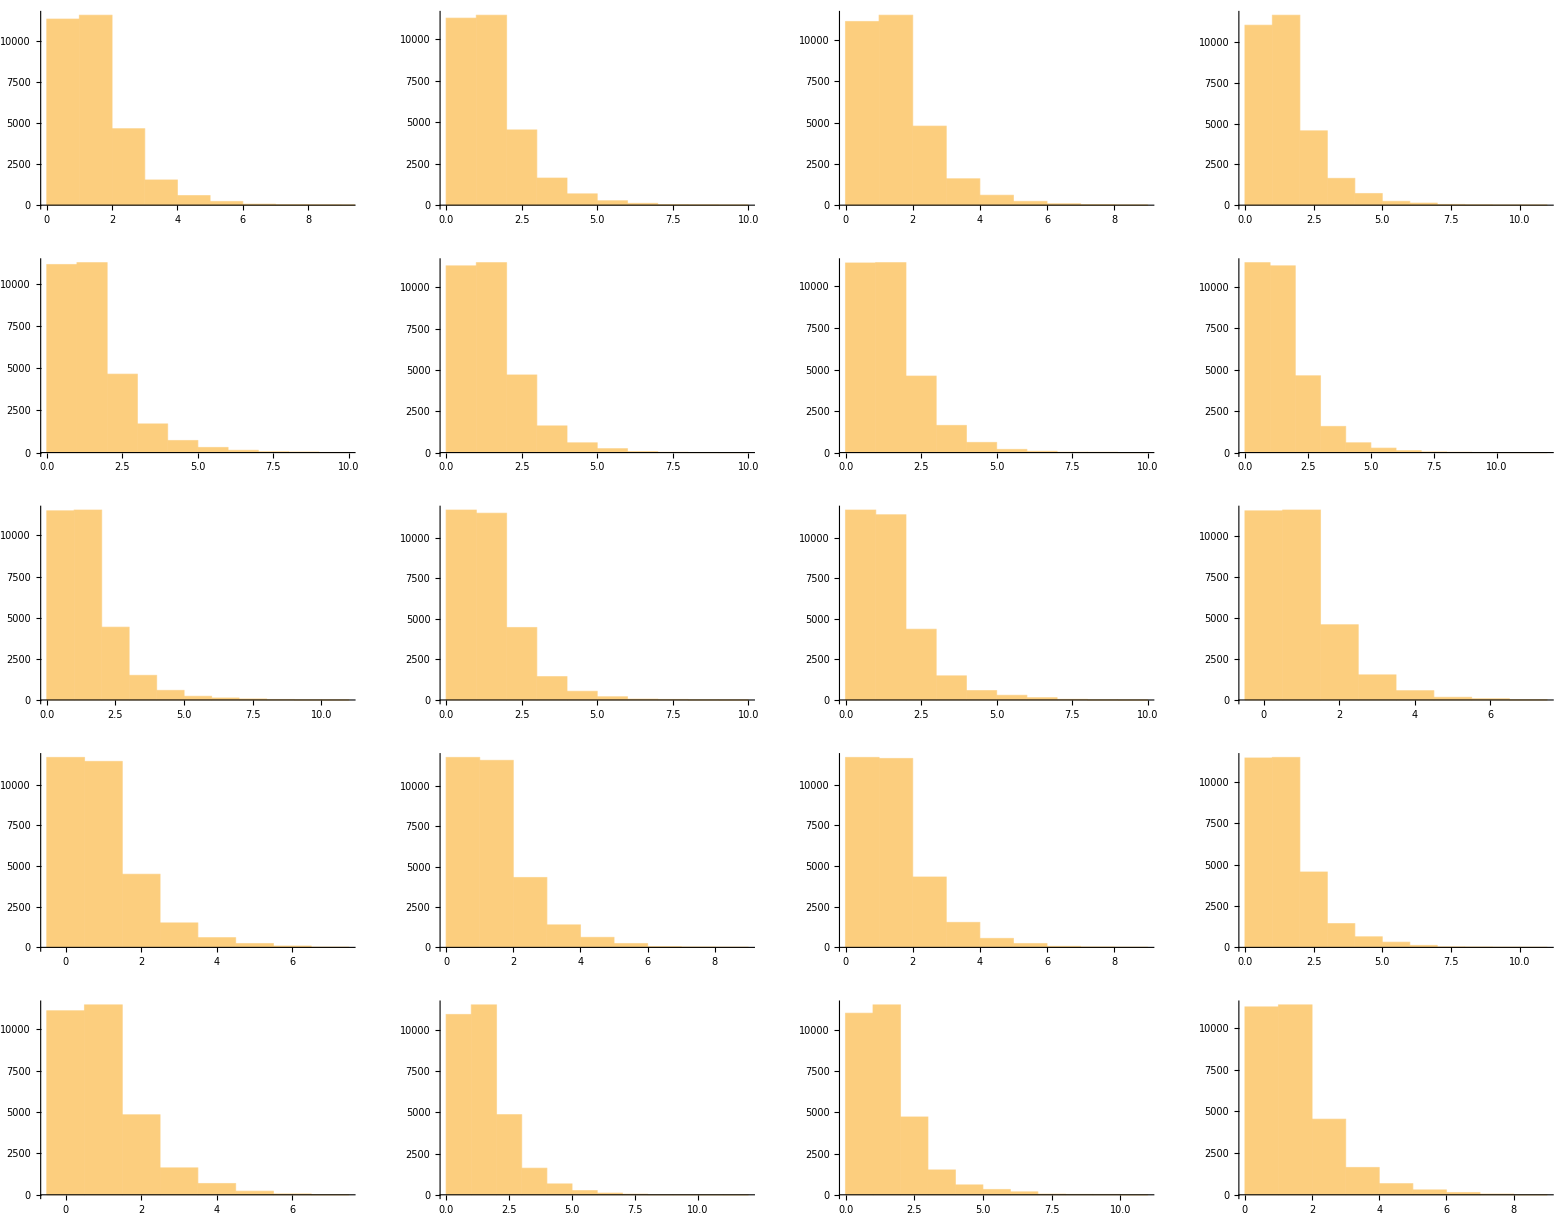

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]]],{i,Length[cicle]}],4]]
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[cicle]}];
```

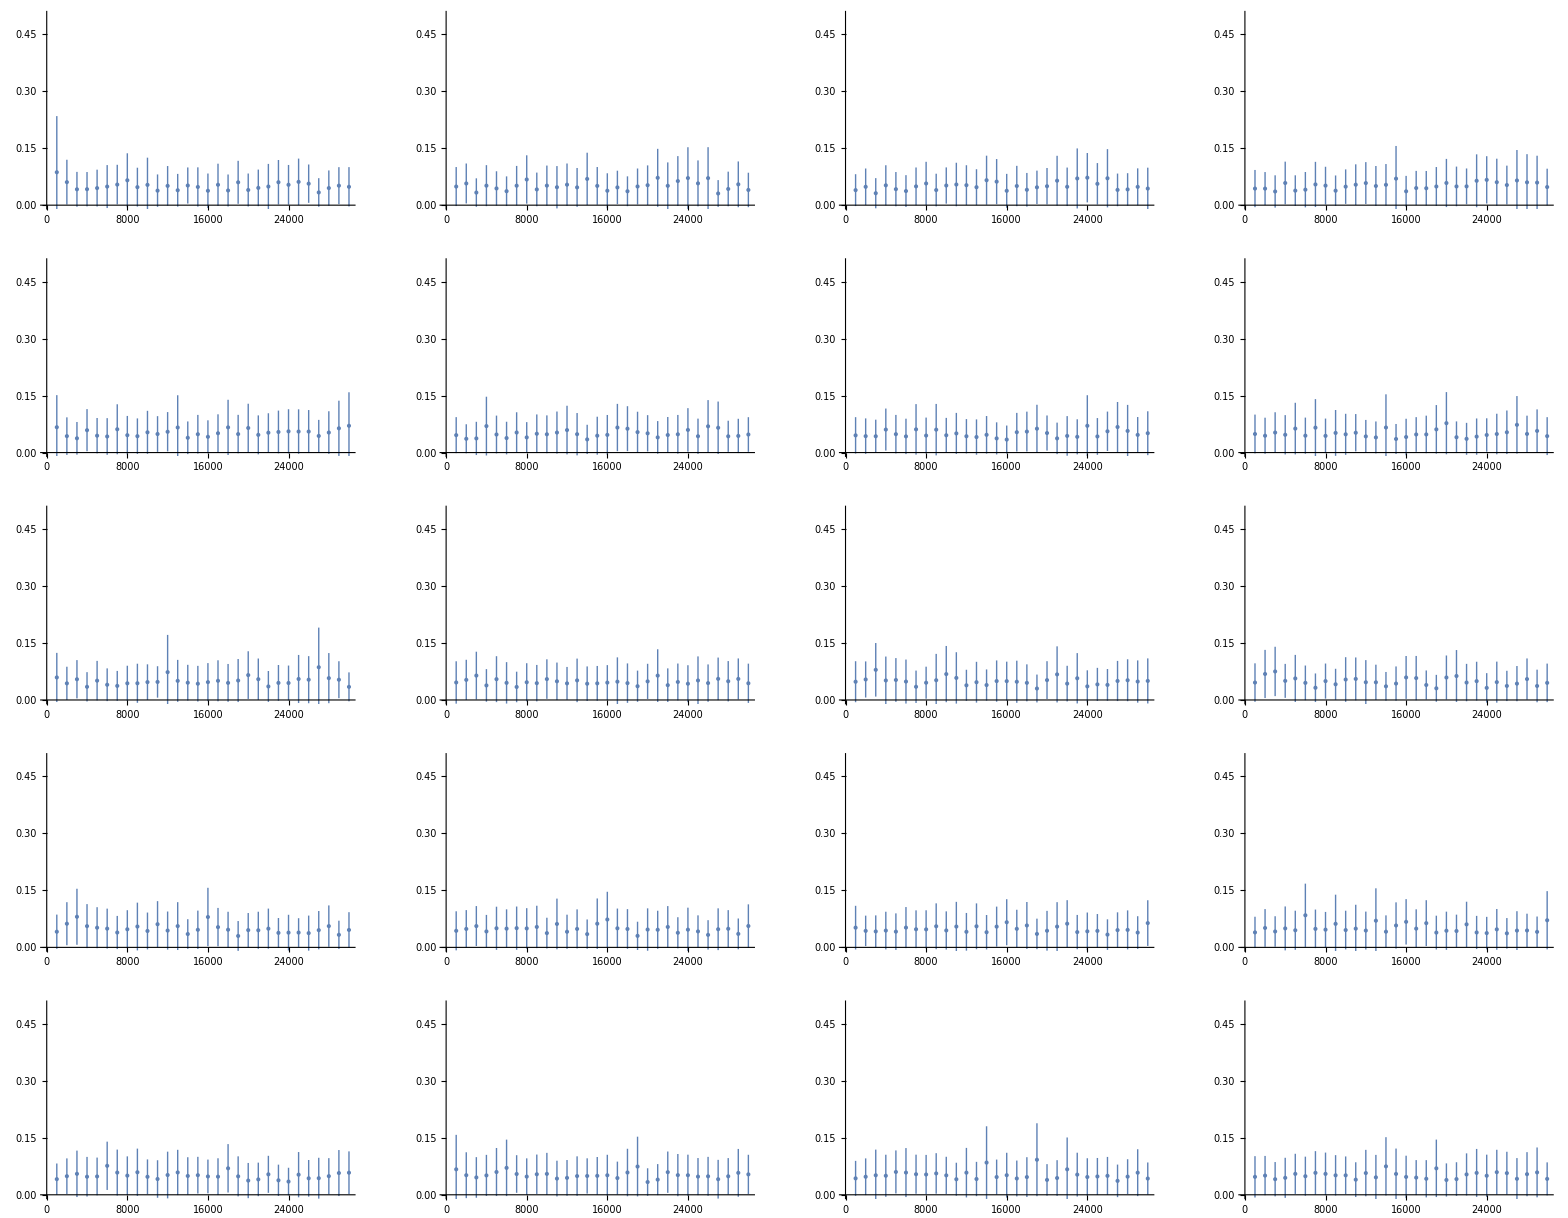

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

## Scale free

#### No lights - all marbles @ node 1

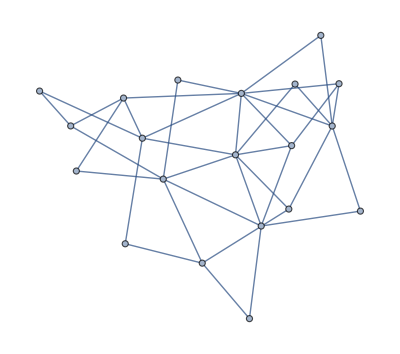

```mathematica
gr=RandomGraph[BarabasiAlbertGraphDistribution[20,2]]
```

```mathematica
VertexDegree[gr]
```

{7,4,8,3,6,5,6,5,4,3,2,2,2,3,2,2,4,2,2,2}

```mathematica
scalefree=graphToNet[gr,{20,1}]
```

{{20,{2,3,6,7,8,11,14}},{0,{1,3,4,6}},{0,{1,2,4,5,8,9,16,20}},{0,{2,3,5}},{0,{3,4,11,13,14,16}},{0,{1,2,7,13,19}},{0,{1,6,10,15,17,20}},{0,{1,3,9,12,18}},{0,{3,8,10,15}},{0,{7,9,12}},{0,{1,5}},{0,{8,10}},{0,{5,6}},{0,{1,5,17}},{0,{7,9}},{0,{3,5}},{0,{7,14,18,19}},{0,{8,17}},{0,{6,17}},{0,{3,7}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[scalefree,ω,ϕ,30000];
```

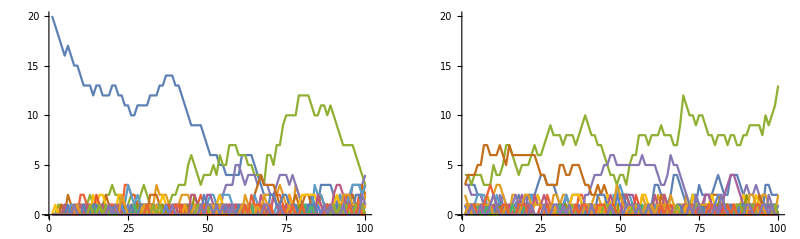

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[scalefree]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[scalefree]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[scalefree]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[scalefree]}],PlotRange->{0,1}]}}]
```

-Graphics-

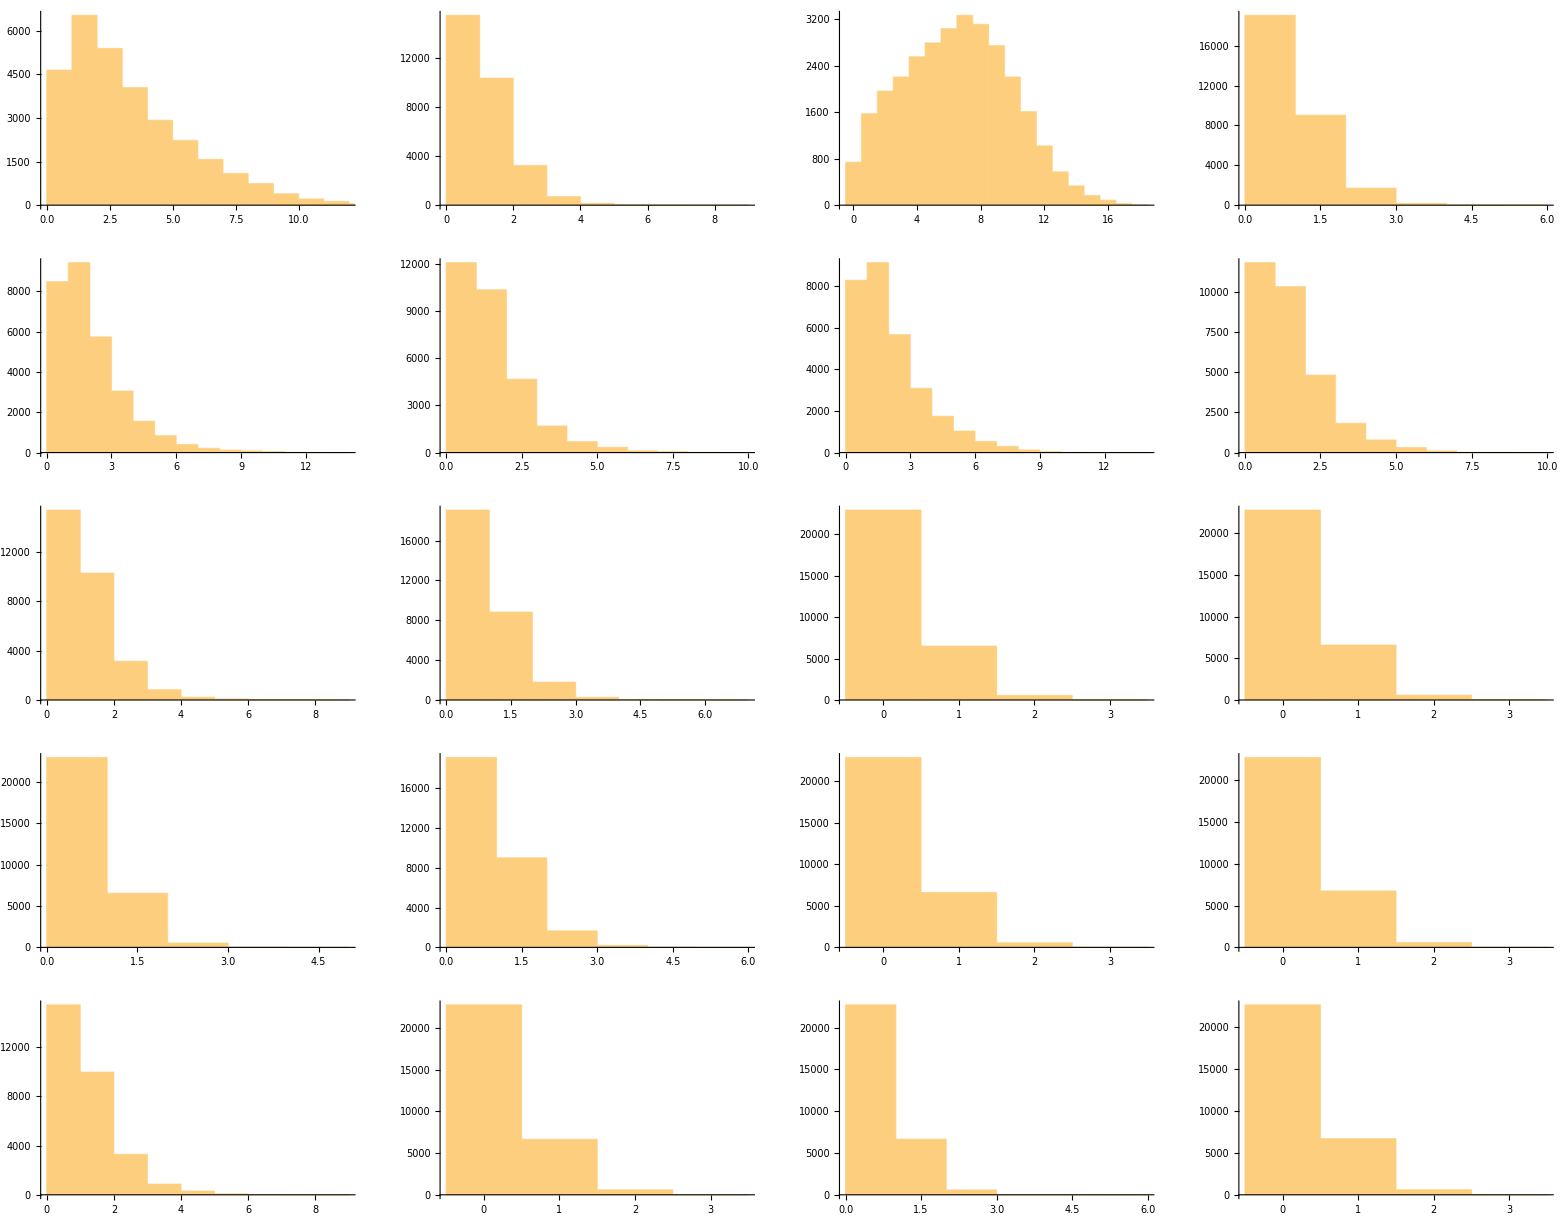

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]]],{i,Length[scalefree]}],4]]
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[scalefree]}];
```

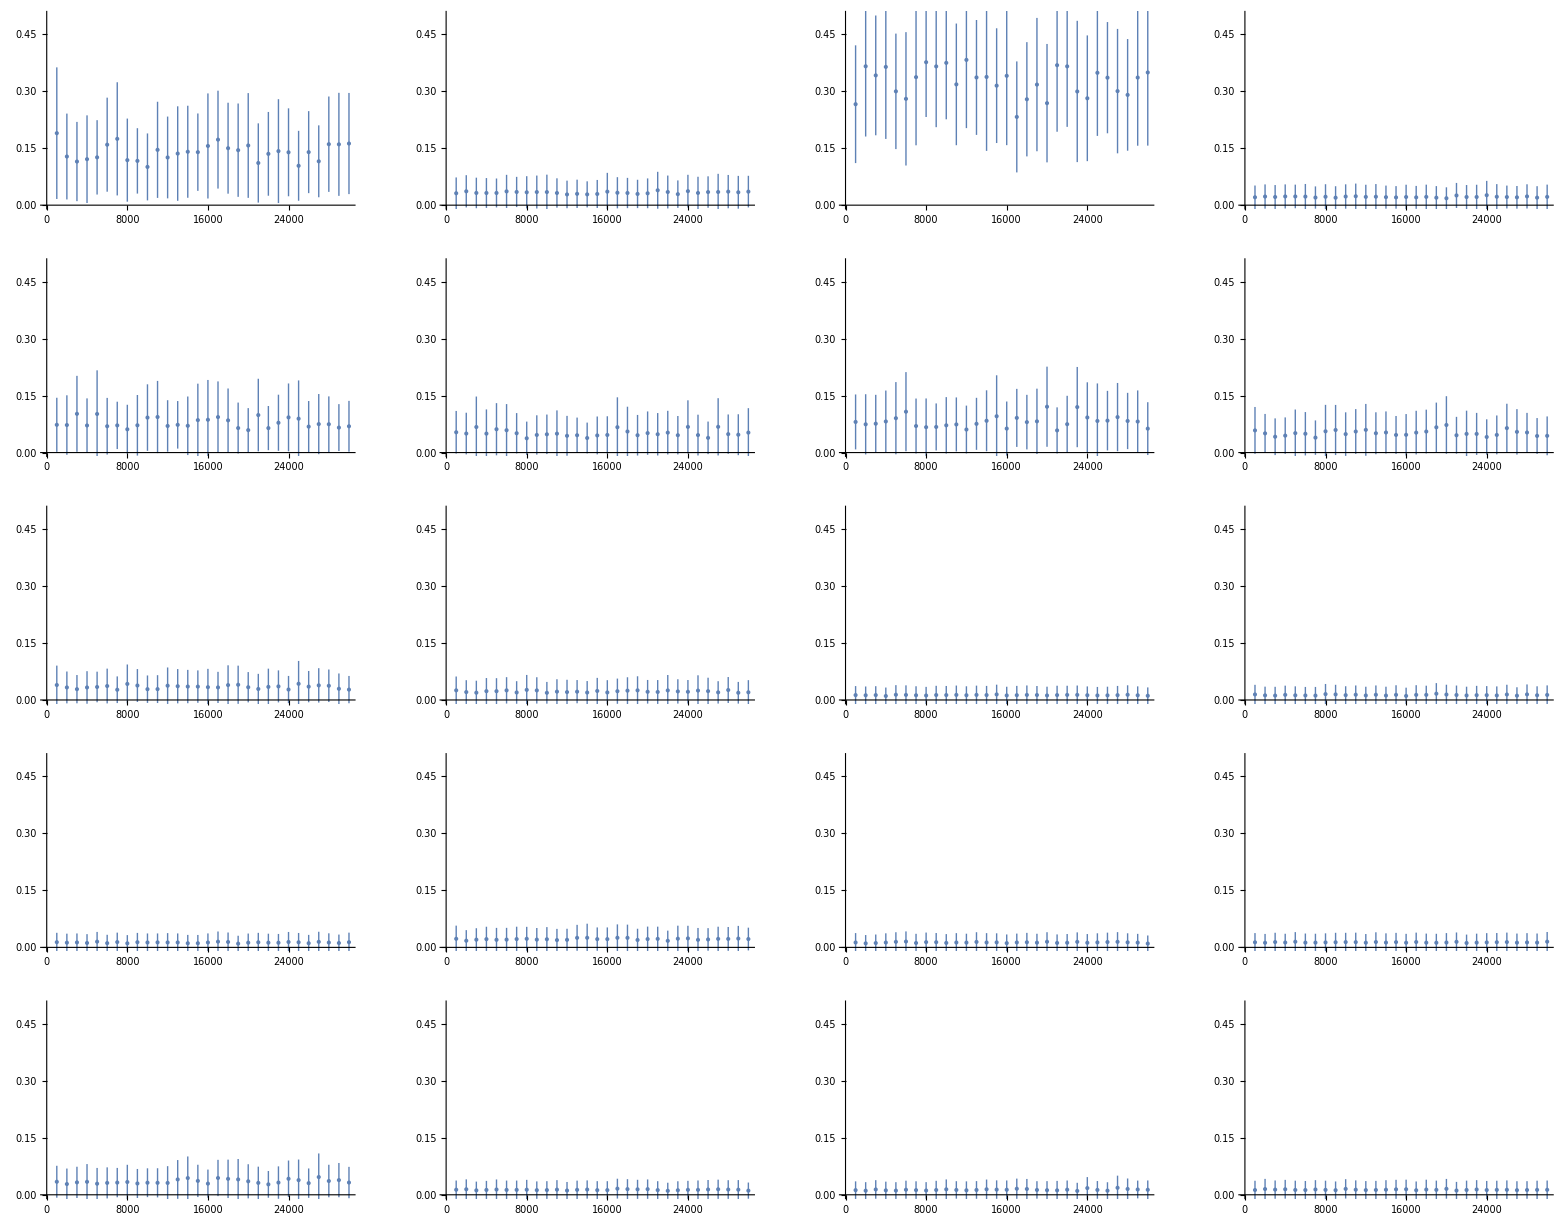

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

## Small world

#### No lights - all marbles @ node 1

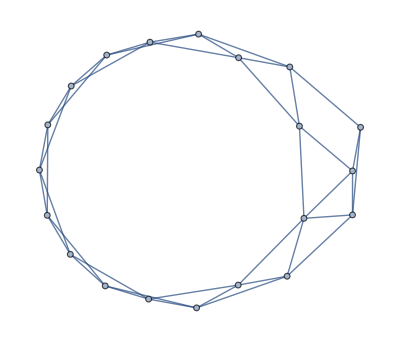

```mathematica
gr=RandomGraph[WattsStrogatzGraphDistribution[20,0.05]]
```

```mathematica
VertexDegree[gr]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,4,4,3}

```mathematica
smallworld=graphToNet[gr,{20,1}]
```

{{20,{2,3,17,19}},{0,{1,3,4,20}},{0,{1,2,4,5}},{0,{2,3,5,6}},{0,{3,4,6,7}},{0,{4,5,7,8}},{0,{5,6,8,9}},{0,{6,7,9,10}},{0,{7,8,10,11}},{0,{8,9,11,12}},{0,{9,10,12,13}},{0,{10,11,13,14}},{0,{11,12,14,15}},{0,{12,13,15,16}},{0,{13,14,16,17}},{0,{14,15,17,18}},{0,{1,15,16,18,19}},{0,{16,17,19,20}},{0,{1,17,18,20}},{0,{2,18,19}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[smallworld,ω,ϕ,30000];
```

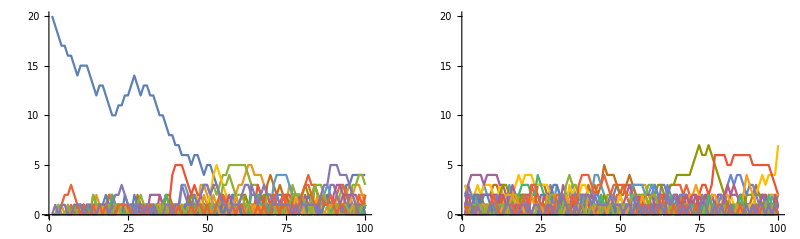

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[smallworld]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[smallworld]}],PlotRange->{0,20}]}}]
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[smallworld]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[smallworld]}],PlotRange->{0,1}]}}]
```

-Graphics-

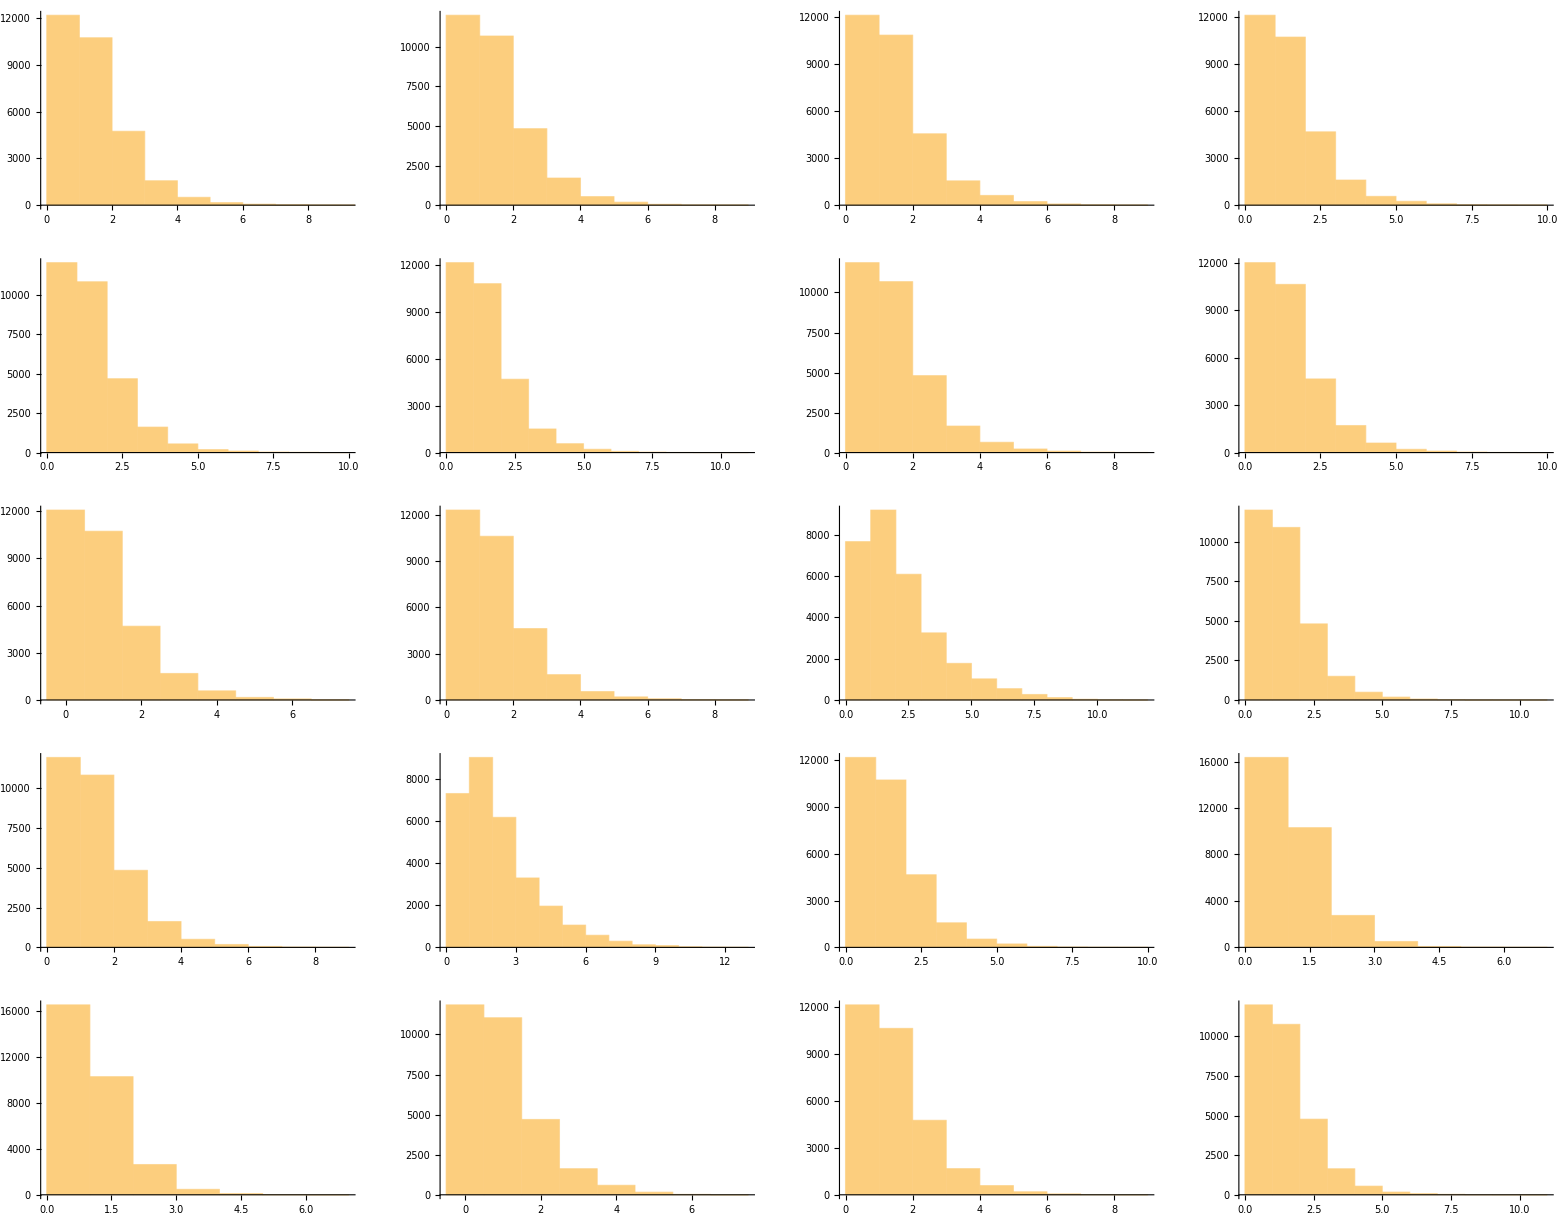

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]]],{i,Length[smallworld]}],4]]
```

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[smallworld]}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

-Graphics-

## Random

#### No lights - all marbles @ node 1

```mathematica
gr=RandomGraph[{20, 40}]
```

-Graphics-

```mathematica
VertexDegree[gr]
```

{5,5,4,3,3,6,3,3,4,4,3,8,4,2,6,3,2,4,3,5}

```mathematica
random=graphToNet[gr,{20,1}]
```

{{20,{4,6,12,15,20}},{0,{7,8,9,16,18}},{0,{6,12,13,15}},{0,{1,15,16}},{0,{12,13,19}},{0,{1,3,10,11,12,18}},{0,{2,10,13}},{0,{2,9,15}},{0,{2,8,11,14}},{0,{6,7,15,16}},{0,{6,9,17}},{0,{1,3,5,6,14,18,19,20}},{0,{3,5,7,15}},{0,{9,12}},{0,{1,3,4,8,10,13}},{0,{2,4,10}},{0,{11,20}},{0,{2,6,12,20}},{0,{5,12,20}},{0,{1,12,17,18,19}}}

```mathematica
ω=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
ϕ=Table[0,{i,Length[cicle]},{j,Length[cicle]}];
marbles=netEvolve[random,ω,ϕ,30000];
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[random]}],PlotRange->{0,20}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[random]}],PlotRange->{0,20}]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/20)[[1;;1000]],100],i],{i,Length[random]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/20,100],i],{i,Length[random]}],PlotRange->{0,1}]}}]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[Histogram[marbles[[All,i]]],{i,Length[random]}],4]]
```

-Graphics-

```mathematica
devs=Table[Table[{i+1000,1/20 Around[Mean[marbles[[All,j]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,j]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}],{j,Length[random]}];
```

```mathematica
GraphicsGrid[Partition[Table[ListPlot[devs[[i]],PlotRange->{0,1/2}],{i,Length[devs]}],4]]
```

-Graphics-

## Complete network

11 nodes, al with degree 10

```mathematica
CompleteGraph[11]
```

-Graphics-

#### No lights - all marbles @ node 1

```mathematica
complete=graphToNet[CompleteGraph[11],{100,1}]
```

{{100,{2,3,4,5,6,7,8,9,10,11}},{0,{1,3,4,5,6,7,8,9,10,11}},{0,{1,2,4,5,6,7,8,9,10,11}},{0,{1,2,3,5,6,7,8,9,10,11}},{0,{1,2,3,4,6,7,8,9,10,11}},{0,{1,2,3,4,5,7,8,9,10,11}},{0,{1,2,3,4,5,6,8,9,10,11}},{0,{1,2,3,4,5,6,7,9,10,11}},{0,{1,2,3,4,5,6,7,8,10,11}},{0,{1,2,3,4,5,6,7,8,9,11}},{0,{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[complete,ω,ϕ,300];
```

```mathematica
marbles//Short
```

{{100,0,0,0,0,0,0,0,0,0,0},«299»,{35,2,12,7,2,23,1,1,1,9,7}}

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
complete=graphToNet[CompleteGraph[11],ConstantArray[100,11]]
```

{{100,{2,3,4,5,6,7,8,9,10,11}},{100,{1,3,4,5,6,7,8,9,10,11}},{100,{1,2,4,5,6,7,8,9,10,11}},{100,{1,2,3,5,6,7,8,9,10,11}},{100,{1,2,3,4,6,7,8,9,10,11}},{100,{1,2,3,4,5,7,8,9,10,11}},{100,{1,2,3,4,5,6,8,9,10,11}},{100,{1,2,3,4,5,6,7,9,10,11}},{100,{1,2,3,4,5,6,7,8,10,11}},{100,{1,2,3,4,5,6,7,8,9,11}},{100,{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[complete,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100 11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Two dense networks joined by a bridge

```mathematica
bridgegrapgh=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,4<->5,6<->7,7<->8,7<->9,7<->10,7<->11,8<->9,8<->10,8<->11,9<->10,9<->11,10<->11},VertexLabels->"Name"]
```

-Graphics-

#### No lights - all marbles @ node 1

```mathematica
bridge=graphToNet[bridgegrapgh,{100,1}]
```

{{100,{2,3,4,5}},{0,{1,3,4,5,6}},{0,{1,2,4,5}},{0,{1,2,3,5}},{0,{1,2,3,4}},{0,{2,7}},{0,{6,8,9,10,11}},{0,{7,9,10,11}},{0,{7,8,10,11}},{0,{7,8,9,11}},{0,{7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[bridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
bridge=graphToNet[bridgegrapgh,ConstantArray[100,11]]
```

{{100,{2,3,4,5}},{100,{1,3,4,5,6}},{100,{1,2,4,5}},{100,{1,2,3,5}},{100,{1,2,3,4}},{100,{2,7}},{100,{6,8,9,10,11}},{100,{7,9,10,11}},{100,{7,8,10,11}},{100,{7,8,9,11}},{100,{7,8,9,10}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[bridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100 11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Two sparse networks joined by a bridge

```mathematica
sparsebridgegraph=Graph[{1<->5,2<->5,3<->5,4<->5,5<->6,6<->7,7<->8,7<->9,7<->10,7<->11},VertexLabels->"Name"]
```

-Graphics-

#### No lights - all marbles @ node 1

```mathematica
sparsebridge=graphToNet[sparsebridgegraph,{100,1}]
```

{{100,{2}},{0,{1,3,4,5,6}},{0,{2}},{0,{2}},{0,{2}},{0,{2,7}},{0,{6,8,9,10,11}},{0,{7}},{0,{7}},{0,{7}},{0,{7}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[sparsebridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/100,100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

#### No lights - marbles all over

```mathematica
sparsebridge=graphToNet[sparsebridgegraph,ConstantArray[100,11]]
```

{{100,{2}},{100,{1,3,4,5,6}},{100,{2}},{100,{2}},{100,{2}},{100,{2,7}},{100,{6,8,9,10,11}},{100,{7}},{100,{7}},{100,{7}},{100,{7}}}

```mathematica
ω=Table[0,{i,Length[complete]},{j,Length[complete]}];
ϕ=Table[0,{i,Length[complete]},{j,Length[complete]}];
marbles=netEvolve[sparsebridge,ω,ϕ,30000];
```

```mathematica
ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/(100  11),100],i],{i,Length[complete]}],PlotRange->{0,1}]
```

-Graphics-

## Tope al número de paquetes que puede haber en un nodo. La regla nueva es, cada nodo tiene una capacidad máxima, en cada tick recibe paquetes si y solo si su capacidad máxima no es superada, si fuera superada no recibe ningún paquete (el número de paquetes debería bajar o permanecer constante)

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,top_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,Length[g]],i,out},
For[i=1,i≤Length[g],i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i,places},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
out=marbles[[-1]]+out;
(*now check if the nodes are all below the top limit*)
out=If[AllTrue[#≤ top&/@out,#&],out,
places=Flatten[Position[out,x_/;x>top]];
places=Flatten[inter/.Rule[#,0]&/@places];
For[i=1;out=ConstantArray[0,n],i≤Length[inter],i++,
If[places[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[places[[i]]]]=out[[places[[i]]]]+1;,
0];
];
marbles[[-1]]+out
];
out
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,{i,T}
];
marbles
]
```

```mathematica
tri=graphToNet[Graph[{1<->2,2<->3,3<->1}],{2,1,2}]
```

{{2,{2,3}},{1,{1,3}},{2,{1,2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
```

```mathematica
marbles=netEvolve[tri,ω,ϕ,10,3];
```

```mathematica
marbles
```

{{2,1,2},{2,1,2},{3,0,2},{2,2,1},{3,2,0},{2,2,1},{2,2,1},{1,3,1},{0,3,2},{1,2,2},{1,2,2}}

```mathematica
Total/@marbles
```

{5,5,5,5,5,5,5,5,5,5,5}

## Triangle

#### No lights - all marbles @ node 1

```mathematica
tri=graphToNet[Graph[{1<->2,2<->3,3<->1}],{3,1}]
```

{{3,{2,3}},{0,{1,3}},{0,{1,2}}}

```mathematica
ω=Table[0,{i,Length[tri]},{j,Length[tri]}];
ϕ=Table[0,{i,Length[tri]},{j,Length[tri]}];
marbles=netEvolve[tri,ω,ϕ,30];
```

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[marbles[[All,i]][[1;;100]],i],{i,Length[tri]}],PlotRange->{0,3}],ListLinePlot[Table[Tooltip[marbles[[All,i]][[-100;;-1]],i],{i,Length[tri]}],PlotRange->{0,3}]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{ListLinePlot[Table[Tooltip[MovingAverage[(marbles[[All,i]]/3)[[1;;1000]],100],i],{i,Length[tri]}],PlotRange->{0,1}],ListLinePlot[Table[Tooltip[MovingAverage[marbles[[All,i]]/3,100],i],{i,Length[tri]}],PlotRange->{0,1}]}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{Histogram[marbles[[All,1]]],Histogram[marbles[[All,2]]],Histogram[marbles[[All,3]]]}}]
```

-Graphics-

```mathematica
Table[{i+1000,Around[Mean[marbles[[All,1]][[i+1;;i+1000]]],StandardDeviation[marbles[[All,1]][[i+1;;i+1000]]]]},{i,0,Length[marbles]-1000,1000}]
```

{{1000,1.00.7},{2000,0.90.7},{3000,1.00.7},{4000,1.00.7},{5000,1.00.7},{6000,1.00.7},{7000,1.00.7},{8000,1.00.7},{9000,1.00.7},{10000,1.00.7},{11000,1.00.7},{12000,1.10.7},{13000,1.00.7},{14000,1.00.7},{15000,1.00.7},{16000,1.00.7},{17000,1.00.7},{18000,1.00.7},{19000,1.00.7},{20000,1.00.7},{21000,1.00.7},{22000,1.00.7},{23000,1.00.7},{24000,1.00.7},{25000,1.00.7},{26000,1.00.7},{27000,1.00.7},{28000,1.00.7},{29000,1.00.7},{30000,1.00.7}}

```mathematica
ListPlot[%,PlotRange->{0,3}]
```

-Graphics-

1. Poner un tope al número de paquetes que puede tener cada nodo (del orden de la media), comparar sin máximo. Calcular el J en todos los casos (fracción de paquetes que se movieron). J Vs. máximo de paquetes.
2. Poner todos semáforos iguales, cambiar la fase en pocos y ver qué pasa con el flujo (# de paquetes por periodo), que fases deben tener para no empeorar.

```mathematica
RandomInteger[10,10]
```

{6,8,4,5,1,1,6,9,9,0}

```mathematica
Position[%1,x_/;x>5]//Flatten
```

{1,2,7,8,9}

```mathematica
Rule[#,0]&/@%13
```

{1→0,2→0,7→0,8→0,9→0}

```mathematica
AllTrue[%,#&]
```

True